# Floating point accuracy effects chaotic solutions

```mathematica
Manipulate[
x0=6.1;y0=6;z0=10;d=10;r=28.24;b=8/3;
sol=NDSolve[{
x'[t]==d (y[t]-x[t]),
y'[t]==r x[t]-y[t]-x[t] z[t],
z'[t]==x[t] y[t]-b z[t],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},AccuracyGoal->n,PrecisionGoal->n];
sol2=NDSolve[{
x'[t]==d (y[t]-x[t]),
y'[t]==r x[t]-y[t]-x[t] z[t],
z'[t]==x[t] y[t]-b z[t],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},AccuracyGoal->10,PrecisionGoal->10];
px=Plot[Evaluate[x[t]/.sol],{t,0,tmax},PlotStyle->Red];
px2=Plot[Evaluate[x[t]/.sol2],{t,0,tmax}];
Show[px,px2,PlotRange-> All,ImageSize->530,LabelStyle->18,AxesLabel-> {t,x[t]}],
Control[{{n,4,"Significant figures"},1,10,ImageSize->Large,Appearance->"Labeled"}],
Control[{{tmax,10,"Time"},5,40,ImageSize->Large,Appearance->"Labeled"}]]
```

## Transient chaos, intermittent chaos, and periodic limit-cycle in the Lorenz system

TRANSIENT CHAOS

-Graphics3D-

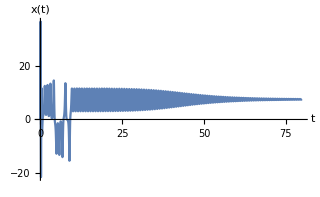
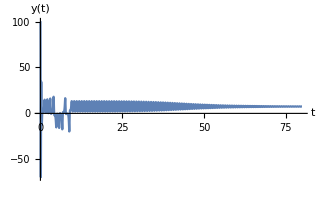
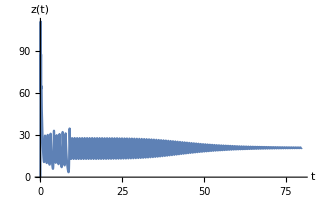

TRANSIENT CHAOS 2

-Graphics3D-

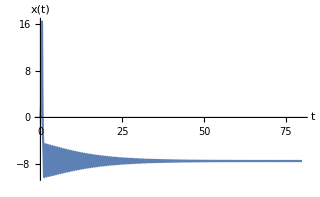
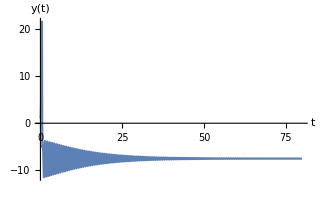
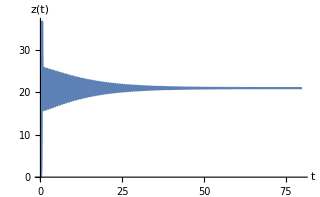

INTERMITTENT CHAOS

-Graphics3D-

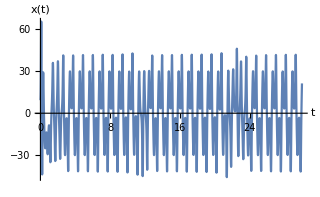
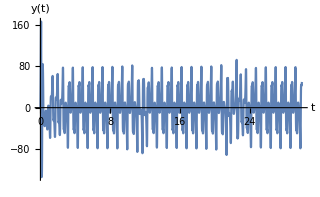
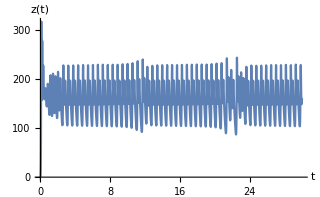

Transient chaos to LIMIT-CYCLE

-Graphics3D-

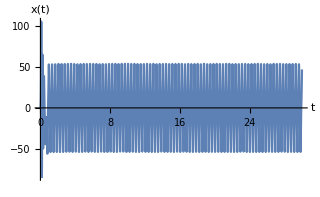
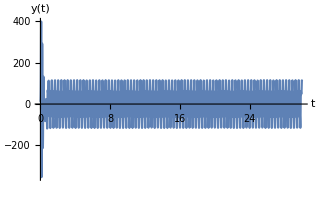
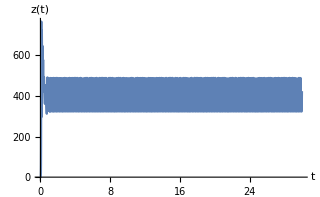

```mathematica
Clear[t,Tmax,x,y,z]
Tmax=80;Tmax2=30;xlimit=22;ylimit=25;nzlimit=2;zlimit=42;
d=10;b=8/3;
(*   FORMAT:      {{x0,y0,z0,r}}*)
TransientICandR={{0,100,0,22}};
Transient2ICandR={{0,1,0,22}};
IntermitICandR={{10,0,0,166.3}};
LimitcycleICandR={{0,10,0,400}};
nint[ic__]:=NDSolve[{x'[t]==d (y[t]-x[t]),y'[t]==ic[[4]] x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-b z[t],
x[0]==ic[[1]],y[0]==ic[[2]],z[0]==ic[[3]]},{x,y,z},{t,0,Tmax},MaxSteps->Infinity]
(*  TRANSIENT CHAOS   *)
Print[Style["TRANSIENT CHAOS",19,Blue]]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.nint/@TransientICandR],{t,0,Tmax},AxesLabel-> {x[t],y[t],z[t]},PlotStyle->{Thin},PlotRange->{{-xlimit,xlimit},{-ylimit,ylimit},{nzlimit,zlimit}},BoxRatios->{1,1,1},PlotPoints->100,ImageSize->430,LabelStyle->18]
Row[{Plot[Evaluate[x[t]/.nint/@TransientICandR],{t,0,Tmax},AxesLabel->{t,x[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[y[t]/.nint/@TransientICandR],{t,0,Tmax},AxesLabel->{t,y[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[z[t]/.nint/@TransientICandR],{t,0,Tmax},AxesLabel->{t,z[t]},PlotRange->All,ImageSize->320,LabelStyle->18]}]
(*  TRANSIENT 2 CHAOS   *)
Print[Style["TRANSIENT CHAOS 2",19,Blue]]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.nint/@Transient2ICandR],{t,0,Tmax},AxesLabel-> {x[t],y[t],z[t]},PlotStyle->{Thin},PlotRange->{{-xlimit,xlimit},{-ylimit,ylimit},{nzlimit,zlimit}},BoxRatios->{1,1,1},PlotPoints->100,ImageSize->430,LabelStyle->18]
Row[{Plot[Evaluate[x[t]/.nint/@Transient2ICandR],{t,0,Tmax},AxesLabel->{t,x[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[y[t]/.nint/@Transient2ICandR],{t,0,Tmax},AxesLabel->{t,y[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[z[t]/.nint/@Transient2ICandR],{t,0,Tmax},AxesLabel->{t,z[t]},PlotRange->All,ImageSize->320,LabelStyle->18]}]
(*  INTERMITTENT  CHAOS   *)
Print[Style["INTERMITTENT CHAOS",19,Blue]]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.nint/@IntermitICandR],{t,0,Tmax2},AxesLabel-> {x[t],y[t],z[t]},PlotStyle->{Thin},PlotRange->{{-55,55},{-100,110},{75,275}},BoxRatios->{1,1,1},PlotPoints->220,ImageSize->430,LabelStyle->18]
Row[{Plot[Evaluate[x[t]/.nint/@IntermitICandR],{t,0,Tmax2},AxesLabel->{t,x[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[y[t]/.nint/@IntermitICandR],{t,0,Tmax2},AxesLabel->{t,y[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[z[t]/.nint/@IntermitICandR],{t,0,Tmax2},AxesLabel->{t,z[t]},PlotRange->All,ImageSize->320,LabelStyle->18]}]
(*  transient to LIMIT-CYCLE   *)
Print[Style["Transient chaos to LIMIT-CYCLE",19,Blue]]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.nint/@LimitcycleICandR],{t,0,Tmax2},AxesLabel-> {x[t],y[t],z[t]},PlotStyle->{Thin},PlotRange->{{-60,60},{-125,125},{300,500}},BoxRatios->{1,1,1},PlotPoints->220,ImageSize->430,LabelStyle->18]
Row[{Plot[Evaluate[x[t]/.nint/@LimitcycleICandR],{t,0,Tmax2},AxesLabel->{t,x[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[y[t]/.nint/@LimitcycleICandR],{t,0,Tmax2},AxesLabel->{t,y[t]},PlotRange->All,ImageSize->320,LabelStyle->18],
Plot[Evaluate[z[t]/.nint/@LimitcycleICandR],{t,0,Tmax2},AxesLabel->{t,z[t]},PlotRange->All,ImageSize->320,LabelStyle->18]}]
```

Creation of this notebook was supported by IT Academy program of Information Technology Foundation for Education (HITSA).